```mathematica
pressureGradient = -10; μ=1;
nGrid = 40+1; Δy=1/(nGrid-1);
y= Table[(i-1)Δy,{i,1,nGrid}];
u = Array["u",nGrid];
```

```mathematica
discreteEqns = Table[
μ (u[[i+1]]-2u[[i]]+u[[i-1]])/Δy^2-pressureGradient==0,
{i,2,nGrid-1}];
```

```mathematica
boundaryConditions = {u[[1]]==0, u[[nGrid]]==0};
```

```mathematica
eqns = Join[discreteEqns,boundaryConditions];
```

```mathematica
sol = NSolve[eqns,u];
```

```mathematica
uVals = u/.sol // #[[1]]&;
```

```mathematica
data = Table[{y[[i]],uVals[[i]]},{i,1,nGrid}];
```

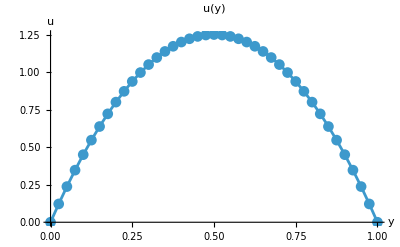

```mathematica
ListLinePlot[data,PlotMarkers->Automatic,AxesLabel->{"y","u"},PlotLabel->"u(y)"]
```

```mathematica
uMean = N[Sum[uVals[[i]],{i,1,nGrid}]]Δy
```

0.832812

```mathematica
uMax = N[Max[uVals]]
```

1.25

```mathematica
uMax/uMean
```

1.50094